```mathematica
Reduce[D[x^2-1/2 Log[x],x]<0&&x>0,x]
```

0<x<1/2

```mathematica
(3-2x)(x+1)^5//Expand
```

3+13 x+20 x^2+10 x^3-5 x^4-7 x^5-2 x^6

```mathematica
Clear[f]
```

```mathematica
f[x]=2x (D[f[x],x]/.x->1)+Log[x]
```

Log[x]+2 x f'[1]

```mathematica
D[f[x],x]
```

1/x+2 f'[1]

```mathematica
r=%;
Solve[(r/.x->1)==f'[1],f'[1]]
```

{{f'[1]→-1}}

```mathematica
Clear[f]
```

```mathematica
f[x_]=Piecewise[{{0, Mod[x,4]==1}, {2, Mod[x,4]==2}, {0, Mod[x,4]==3}, {-2, Mod[x,4]==0}}]
```

Piecewise[{{0, Mod[x,4]==1}, {2, Mod[x,4]==2}, {0, Mod[x,4]==3}, {-2, Mod[x,4]==0}, {0, True}}]

```mathematica
∑_(n=1)^50 f[n]
```

2

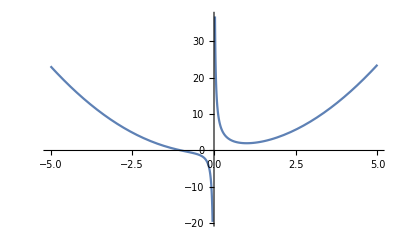

```mathematica
Plot[x^2-Log[Abs[x]]+1/x,{x,-5,5}]
```

```mathematica
2 3! Binomial[3,1] 2!
```

72

```mathematica
Reduce[a x+1≤x-2&&1/2≤x≤1,a]
```

1/2≤x≤1&&a≤(-3+x)/x

```mathematica
Minimize[{(-3+x)/x,1/2≤x≤1},x]
```

{-5,{x→1/2}}

```mathematica
D[x^2 Cos[x],x]
```

2 x Cos[x]-x^2 Sin[x]

```mathematica
Clear[f,a]
```

```mathematica
f[x_]=(-3^x+a)/(3^(x+1)+b)
```

(-3^x+a)/(3^(1+x)+b)

```mathematica
a=b=1
```

1

```mathematica
Solve[f[x]==3^x,x]
```

{{x→ConditionalExpression[-1+(2 ⅈ π C[1])/Log[3], C[1]∈ℤ]},{x→ConditionalExpression[(ⅈ π)/Log[3]+(2 ⅈ π C[1])/Log[3], C[1]∈ℤ]}}

```mathematica
Clear[f]
```

```mathematica
f[x_]=(x-k)E^x
```

ⅇ^x (-k+x)

```mathematica
Reduce[D[f[x],x]==0&&D[f[x],{x,2}]≠0,x]
```

x==-1+k

```mathematica
D[f[x],{x,2}]/.x->-1+k
```

ⅇ^(-1+k)

```mathematica
Manipulate[
Plot[(x-k)E^x,{x,-1.3,1.3}
],
{k,-10,10}
]
```